# Numerical Derivative

## Sampled functions

```mathematica
?dataDerivative
```

```mathematica
h=π/1000.
```

0.00314159

```mathematica
data=Table[{x,Sin[x]},{x,0.,2π,h}];
```

```mathematica
{df,df2}=Transpose[Table[{Cos[x],-Sin[x]},{x,0,2π,h}]];
```

### FDD (1)

```mathematica
ffd1=dataDerivative[data];
```

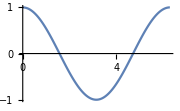

```mathematica
ListLinePlot[ffd1,ImageSize->Small]
```

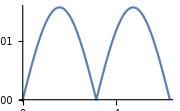

```mathematica
ListLinePlot[Abs[ffd1[[All,2]]-df[[;;-2]]],
DataRange->{data[[1,1]],data[[-2,1]]},ImageSize->Small]
```

### BFD (1)

```mathematica
bfd1=dataDerivative[data,"FDMethod"->"Backward"];
```

```mathematica
ListLinePlot[bfd1,ImageSize->Small]
```

-Graphics-

### Roundoff vs truncation

#### Ejemplo 1

```mathematica
Sin'[1.]//InputForm
```

0.5403023058681398

```mathematica
FDDerivative[Sin[x],x,1.,0.01]//InputForm
```

0.536085981011869

```mathematica
NumberForm[TableForm[Table[FDDerivative[Sin[x],x,1.,10^-a],{a,1,20}]],{17,16}]
```

0.4973637525353891
0.5360859810118690
0.5398814803603269
0.5402602314186211
0.5402980985058647
0.5403018851213304
0.5403022640404487
0.5403023028982545
0.5403023584094058
0.5403022473871033
0.5403011371640787
0.5403455460850637
0.5395683899678261
0.5440092820663267
0.5551115123125783
0.0000000000000000
0.0000000000000000
0.0000000000000000
0.0000000000000000
0.0000000000000000

#### Ejemplo 2

```mathematica
exact=Sin'[π/4.];
```

```mathematica
exact//InputForm
```

0.7071067811865476

```mathematica
tabla=Table[{10.^-n,Abs[FDDerivative[Sin[x],{x,1},π/4.,10^-n]-exact]},{n,1,20}];
```

```mathematica
tabla//TableForm
```

0.1 | 0.0365038
0.01 | 0.00354729
0.001 | 0.000353671
0.0001 | 0.0000353565
0.00001 | 3.53555×10^-6
1.×10^-6 | 3.53553×10^-7
1.×10^-7 | 3.69178×10^-8
1.×10^-8 | 8.05198×10^-9
1.×10^-9 | 7.46654×10^-8
1.×10^-10 | 1.85688×10^-7
1.×10^-11 | 5.7368×10^-6
1.×10^-12 | 0.000116759
1.×10^-13 | 0.000105285
1.×10^-14 | 0.00766628
1.×10^-15 | 0.040973
1.×10^-16 | 0.707107
1.×10^-17 | 0.707107
1.×10^-18 | 0.707107
1.×10^-19 | 0.707107
1.×10^-20 | 0.707107

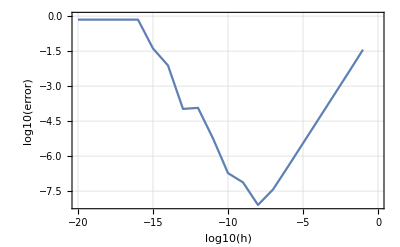

```mathematica
ListLinePlot[Log[10,tabla],Frame->True,FrameLabel->{"log10(h)","log10(error)"},GridLines->Automatic]
```

```mathematica
minErrorDerivative[Sin[u],{u,1},π/4.,"InitialStep"->0.5,"ShrinkageFactor"->1.1]
```

0.707107

# Pregunta 3 Tarea 4

```mathematica
x[t_]:=Sin[t](Exp[Cos[t]]-2Cos[4.t]+Sin[t/12]^5)
y[t_]:=Cos[t](Exp[Cos[t]]-2Cos[4.t]+Sin[t/12]^5)
```

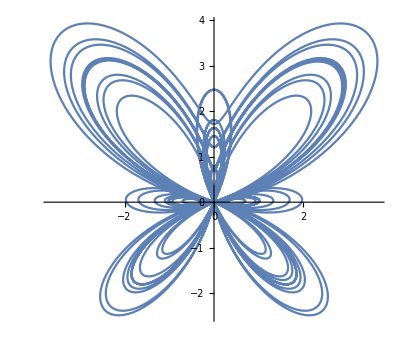

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,21 π}]
```

#### Esta funcion toma una muestra de N ( NumPoints) puntos entre tmin y tmax, y luego calcula las derivadas de x[t] y y[t] en cada uno de esos puntos sampleados . Luego de esos puntos realiza dos interpolaciones de x'[t] y y'[t] y con esas funciones de interpolacion calculamos la longitud de arco con NIntegrate y la formula de longitud de arco. La funcion tiene 4 opciones, 2 opciones corresponden a las opciones de minErrorDerivative y las otras 2 al metodo de interpolacion y el numero de puntos para interpolar.

```mathematica
Options[LengthArc]={"InitialStep"->0.01,"ShrinkageFactor"->1.4,"InterpolationMethod"->"Spline","NumPoints"->800};
```

```mathematica
LengthArc[{x1_,y1_},tmin_,tmax_,opts:OptionsPattern[]]:=
Module[{h0,sF,method,numPoints, datadXdt,datadYdt,dxdtInterp,dydtInterp,u,arclength},
h0=OptionValue["InitialStep"];(*Initial step h for derivative*)
sF=OptionValue["ShrinkageFactor"];(*shrinkage factor for derivative*)
method=OptionValue["InterpolationMethod"];(*interpolation method for data of derivatives*)
numPoints=OptionValue["NumPoints"];(*number of points to sample from the derivative to then interpolate*)

datadXdt=Array[{#,minErrorDerivative[x1[u],{u,1},#,"InitialStep"->h0,"ShrinkageFactor"->sF]}&,numPoints,{tmin,tmax}];(*Generate data of {t,x'[t]}*)
datadYdt=Array[{#,minErrorDerivative[y1[u],{u,1},#,"InitialStep"->h0,"ShrinkageFactor"->sF]}&,numPoints,{tmin,tmax}];
(*Generate data of {t,y'[t]}*)

dxdtInterp=Interpolation[datadXdt,Method->method];(*interpolate data x'[t]*)
dydtInterp=Interpolation[datadYdt,Method->method];(*interpolate data y'[t]*)

arclength=NIntegrate[√(dxdtInterp[t]^2+dydtInterp[t]^2),{t,tmin,tmax}];(*Function for arc length*)
arclength
]
```

```mathematica
ArcLen=LengthArc[{x,y},0.,21π,"InitialStep"->0.1,"ShrinkageFactor"->1.5,"NumPoints"->1000]
```

375.394

```mathematica
Options[CurvatureRadius]={"InitialStep"->0.01,"ShrinkageFactor"->1.4,"InterpolationMethod"->"Spline","NumPoints"->800};
```

```mathematica
CurvatureRadius[{x1_,y1_},tmin_,tmax_,opts:OptionsPattern[]]:=
Module[{h0,sF,method,numPoints, datadXdt,datadYdt,datadX2dt2,datadY2dt2,dxdtInterp,dx2dt2Interp,dydtInterp,dy2dt2Interp,u,curvatureData,CurveInterp},
h0=OptionValue["InitialStep"];(*Initial step h for derivative*)
sF=OptionValue["ShrinkageFactor"];(*shrinkage factor for derivative*)
method=OptionValue["InterpolationMethod"];(*interpolation method for data of derivatives*)
numPoints=OptionValue["NumPoints"];(*number of points to sample from the derivative to then interpolate*)

datadXdt=Array[{#,minErrorDerivative[x1[u],{u,1},#,"InitialStep"->h0,"ShrinkageFactor"->sF]}&,numPoints,{tmin,tmax}];(*Generate data of {t,x'[t]}*)
datadX2dt2=Array[{#,minErrorDerivative[x1[u],{u,2},#,"InitialStep"->h0,"ShrinkageFactor"->sF]}&,numPoints,{tmin,tmax}];(*Generate data of {t,x''[t]}*)
datadYdt=Array[{#,minErrorDerivative[y1[u],{u,1},#,"InitialStep"->h0,"ShrinkageFactor"->sF]}&,numPoints,{tmin,tmax}];
(*Generate data of {t,y'[t]}*)
datadY2dt2=Array[{#,minErrorDerivative[y1[u],{u,2},#,"InitialStep"->h0,"ShrinkageFactor"->sF]}&,numPoints,{tmin,tmax}];
(*Generate data of {t,y''[t]}*)

(*Formula for radius of curvature*)
curvatureData=Abs[(datadXdt[[;;,2]]^2+datadYdt[[;;,2]]^2)^(3/2)/(datadXdt[[;;,2]]*datadY2dt2[[;;,2]]-datadYdt[[;;,2]]*datadX2dt2[[;;,2]])];
(*Interpolate the curvature data points*)
CurveInterp=Interpolation[Partition[Riffle[datadXdt[[;;,1]],curvatureData],2],Method->method];
CurveInterp
]
```

```mathematica
curveInt=CurvatureRadius[{x,y},0.,21π,"NumPoints"->3000]
```

InterpolatingFunction[…]

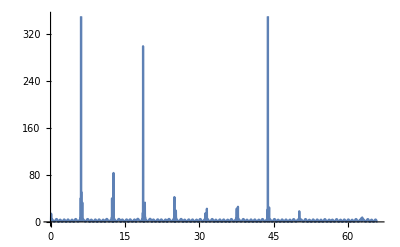

```mathematica
Plot[curveInt[u],{u,0.,21π},PlotRange->{Automatic,{0,350}}]
```

```mathematica
TrueArcLength[θ_]:=Evaluate[ArcCurvature[{x[θ],y[θ]},θ]]
```

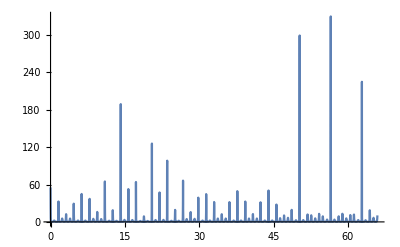

```mathematica
Plot[TrueArcLength[θ],{θ,0,21π},PlotRange->All]
```